## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
(* SAVE TO H5 FOR PySR*)
(*PbbsqA2Bvalueserrbars[ampname_,P1_,etavalue_]:=(
PbbsqA2BvalueerrbarLIST={};
PbaveragedbsquareA2B=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],{Pb32by2Pi, bsquare,data}];
forMakeErrBars = {};
Do[
AppendTo[forMakeErrBars,{{PbaveragedbsquareA2B[[i]][[1]]*(2*N[Pi]/32),PbaveragedbsquareA2B[[i]][[2]]},PbaveragedbsquareA2B[[i]][[3]]}],{i, Length[PbaveragedbsquareA2B]}];
PbbsqA2Bvalueerrbar = MakeErrBars[forMakeErrBars];
Do[
AppendTo[PbbsqA2BvalueerrbarLIST, {etavalue, PbbsqA2Bvalueerrbar[[i]][[1]][[1]][[1]] ,PbbsqA2Bvalueerrbar[[i]][[1]][[1]][[2]],  PbbsqA2Bvalueerrbar[[i]][[1]][[2]],  PbbsqA2Bvalueerrbar[[i]][[2]][[1]][[2]]}];
,{i, Length[PbbsqA2Bvalueerrbar]}];
Return[PbbsqA2BvalueerrbarLIST]
)
ExporttoH5Amp[ampname_,P1_]:=(
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_Pb_bsquare_Amp_Re__Im_err.h5",Table["Pl"<>ToString[P1]<>"/eta_"<>ToString[n]<>"_Pb_bsq_Im"<>ToString[ampname]<>"_err"->PbbsqA2Bvalueserrbars[ampname, P1, n],{n,1,10}],OverwriteTarget->"Append"];
Import["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_Pb_bsquare_Amp_Re_Im__err.h5","StructureGraph"]
)
Do[ExporttoH5Amp[A2B,-i],{i, 1,4}]*)
```

```mathematica
Import["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_Pb_bsquare_Amp_Re_Im_err.h5","StructureGraph"]
```

-Graphics-

```mathematica
PlotAbLfordiffbLbT[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bL]];
PlotbLforDiffbTList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->bnum}],{bL,data}];
AppendTo[PlotbLforDiffbTList,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{, Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bL_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbL,"PDF",ImageResolution->600];
PlotbTforDiffbLList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bL->bLi, bNum->bnum}],{bT,data}];
AppendTo[PlotbTforDiffbLList,bLAmp];
 ,{bLi,bLlist}];
PlotbT= ErrorListPlot[Table[MakeErrBars[PlotbTforDiffbLList[[bLi]]],{bLi, Length[bLlist]}],FrameLabel->{,ampname b bnum}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bLlist[[bLi]]],{bLi,Length[bLlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bT_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbT,"PDF",ImageResolution->600];GraphicsRow[{PlotbL,PlotbT},ImageSize->Full]
)
PlotAfordiffBPbbsq[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
bsquarelist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bsquare]];
(*bsquarelist = Select[fullbsquarelist,8<=#<=25&];*)
Pb32by2Pilist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],Pb32by2Pi]];
PlotPbforDiffbsq={};
Do[
PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi, bNum->bnum}],{Pb32by2Pi,data}];
AppendTo[PlotPbforDiffbsq,PbAmp];
 ,{bsqi,bsquarelist}];
PlotbP= ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsq[[bsqi]]],{bsqi, Length[bsquarelist]}],FrameLabel->{ , Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bsquarelist[[bsqi]]],{bsqi,Length[bsquarelist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bP_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->bnum}],{bsquare,data}];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bsq_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotbsq,"PDF",ImageResolution->600];
GraphicsRow[{PlotbP,Plotbsq},ImageSize->Full]
)
```

```mathematica
PlotAbLfordiffbLbT[A12B,-1,8, even, "Re"]
```

Re A12B =>  = -1 ,eta = 8

-Graphics-

```mathematica
PlotAfordiffBPbbsq[A12B,-1,8, even]
PlotAfordiffBPbbsq[A2B,-1,8, even]
PlotAfordiffBPbbsq[A12B,-1,8, odd]
PlotAfordiffBPbbsq[A2B,-1,8, odd]
```

A12B b even =>  = -1 ,eta = 8

-Graphics-

A2B b even =>  = -1 ,eta = 8

-Graphics-

A12B b odd =>  = -1 ,eta = 8

-Graphics-

A2B b odd =>  = -1 ,eta = 8

-Graphics-

-Graphics-

```mathematica
Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->-1,etav->8}],{bsquare,Pb32by2Pi}]]
```

{{1,0},{2,-1},{2,1},{4,0},{5,-2},{5,-1},{5,1},{5,2},{8,-2},{8,2},{9,0},{16,0},{17,-4},{17,4},{18,-3},{18,3},{20,-4},{20,-2},{20,2},{20,4},{25,0},{32,-4},{32,4},{36,0},{45,-6},{45,-3},{45,3},{45,6},{49,0},{50,-5},{50,5},{68,-8},{68,8}}

```mathematica
PlotAfordiffBPbbsq[A12B,-1,8]
PlotAfordiffBPbbsq[A12B,-2,8]
PlotAfordiffBPbbsq[A12B,-3,8]
PlotAfordiffBPbbsq[A12B,-4,8]
```

PlotAfordiffBPbbsq[A12B,-1,8]

PlotAfordiffBPbbsq[A12B,-2,8]

PlotAfordiffBPbbsq[A12B,-3,8]

PlotAfordiffBPbbsq[A12B,-4,8]

```mathematica
PlotAfordiffBPbbsq[A2B,-1,8]
PlotAfordiffBPbbsq[A2B,-2,8]
PlotAfordiffBPbbsq[A2B,-3,8]
PlotAfordiffBPbbsq[A2B,-4,8]
```

PlotAfordiffBPbbsq[A2B,-1,8]

PlotAfordiffBPbbsq[A2B,-2,8]

PlotAfordiffBPbbsq[A2B,-3,8]

PlotAfordiffBPbbsq[A2B,-4,8]

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];
```

```mathematica
modelsechfit[x1_,x2_,{a_,b_,c_}]:=a*Sech[b*x1]*(1/(c+x2));
FitAfordiffBPbbsq[ampname_,P1_, etavalue_, modelfit_]:=(
dataforfit = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->even}],{Pb32by2Pi, bsquare,data}];
fitJK =JackknifeFit3D[dataforfit,modelfit[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfit];
fitParas=FitParameters/. fitJK;
fitchiDoF=chisquareDoF/. fitJK;
fita = meanfromJK[fitParas[[1]]];
fitb = meanfromJK[fitParas[[1]]];
fitc = meanfromJK[fitParas[[1]]];
Print["Re",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF,"\n Plotting just the mean value of Jackknife fit !\n"];
bsquarelist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->even}],bsquare]];
Pb32by2Pilist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->even}],Pb32by2Pi]];
PlotPbforDiffbsq={};
Do[
PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi, bNum->even}],{Pb32by2Pi,data}];
AppendTo[PlotPbforDiffbsq,PbAmp];
 ,{bsqi,bsquarelist}];
PlotbP= ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsq[[bsqi]]],{bsqi, Length[bsquarelist]}],FrameLabel->{ , ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bsquarelist[[bsqi]]],{bsqi,Length[bsquarelist]}]];
fitPlotbP=Show[PlotbP,Table[Plot[modelfitJackkife[modelfit, fitParas, Pbx,bsquarelist[[bsqi]]][[1]],{Pbx,Min[Pb32by2Pilist],Max[Pb32by2Pilist]},PlotStyle->ColorData[97,"ColorList"][[Mod[bsqi,15]]]],{bsqi,Length[bsquarelist]}]];
Print[fitPlotbP];
Export["/Users/hariprashadravikumar/Downloads/Pbfit_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->even}],{bsquare,data}];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}]];
Print[modelfitJackkife[modelfit, fitParas, 1,0.1][[1]]];
fitPlotbsq=Show[Table[Plot[modelfitJackkife[modelfit, fitParas, Pb32by2Pilist[[Pbi]],bsqx][[1]],{bsqx,Min[bsquarelist],Max[bsquarelist]},PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[Mod[Pbi,15]]]],{Pbi,Length[Pb32by2Pilist]}],Plotbsq];
Print[fitPlotbsq];
Export["/Users/hariprashadravikumar/Downloads/bsqfit_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbsq,"PDF",ImageResolution->600];
)
```

ReA12B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.0926(76)⟩_(2902J), ⟨0.197(48)⟩_(2902J), ⟨0.484(77)⟩_(2902J)}
 chisquareDoF = 7.13467
 Plotting just the mean value of Jackknife fit !

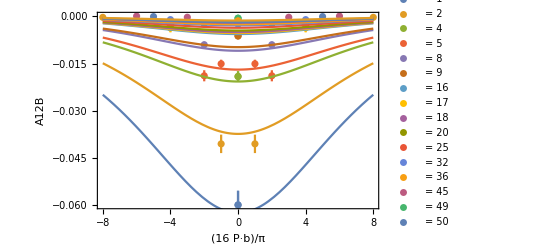

-0.15449

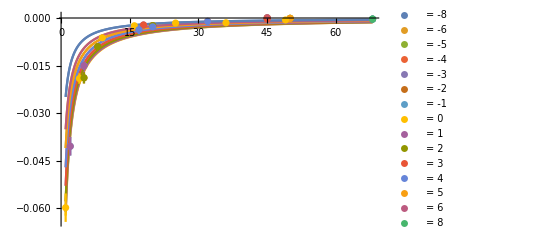

```mathematica
FitAfordiffBPbbsq[A12B, -1, 8, modelsechfit]
```

ReA2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.4024(25)⟩_(2902J), ⟨0.3922(50)⟩_(2902J), ⟨0.6377(20)⟩_(2902J)}
 chisquareDoF = 255.477
 Plotting just the mean value of Jackknife fit !

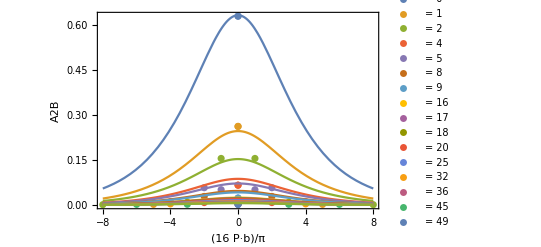

0.50609

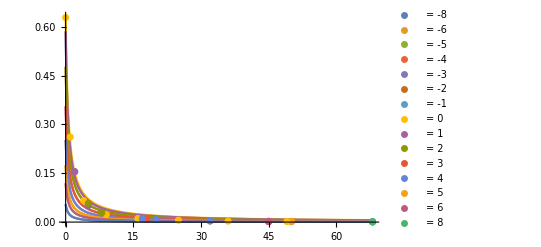

```mathematica
FitAfordiffBPbbsq[A2B, -1, 8, modelsechfit]
```

A12B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨-0.0893(56)⟩_(2902J), ⟨-1.95(69)⟩_(2902J), ⟨0.073(36)⟩_(2902J)}
 chisquareDoF = 13.9337
 Plotting just the mean value of Jackknife fit !

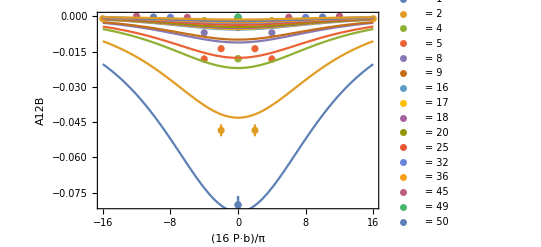

-0.509007

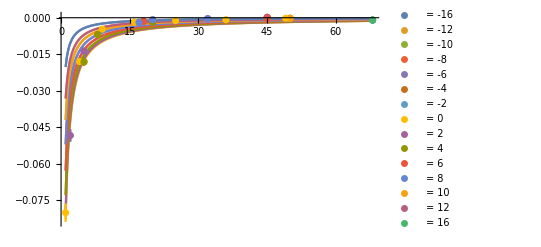

```mathematica
FitAfordiffBPbbsq[A12B, -2, 8, modelsechfit]
```

ReA2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨0.3547(35)⟩_(2902J), ⟨0.1971(37)⟩_(2902J), ⟨0.5630(28)⟩_(2902J)}
 chisquareDoF = 149.779
 Plotting just the mean value of Jackknife fit !

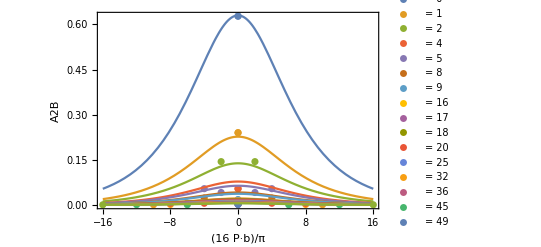

0.524759

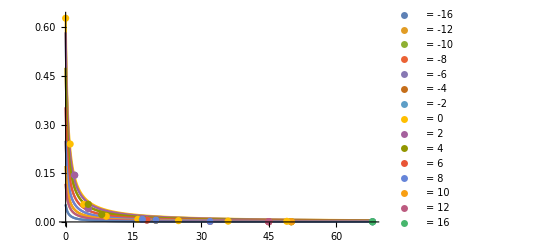

```mathematica
FitAfordiffBPbbsq[A2B, -2, 8, modelsechfit]
```

```mathematica
modelsechfitIm[x1_,x2_,{a_,b_,c_}]:=a*x1*Exp[-b*x1^2]*(1/(c+x2));
FitImAfordiffBPbbsq[ampname_,P1_, etavalue_, modelfit_]:=(
dataforfit = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],{Pb32by2Pi, bsquare,data}];
(*dataforfit=Select[dataforfitfull,#[[2]]!=0&];*)
fitJK =JackknifeFit3D[dataforfit,modelfit[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfit];
fitParas=FitParameters/. fitJK;
fitchiDoF=chisquareDoF/. fitJK;
fita = meanfromJK[fitParas[[1]]];
fitb = meanfromJK[fitParas[[1]]];
fitc = meanfromJK[fitParas[[1]]];
Print["Im",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF,"\n Plotting just the mean value of Jackknife fit !\n"];
bsquarelist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],bsquare]];
Pb32by2Pilist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],Pb32by2Pi]];
PlotPbforDiffbsq={};
Do[
PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi, bNum->odd}],{Pb32by2Pi,data}];
AppendTo[PlotPbforDiffbsq,PbAmp];
 ,{bsqi,bsquarelist}];
PlotbP= ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsq[[bsqi]]],{bsqi, Length[bsquarelist]}],FrameLabel->{ , ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bsquarelist[[bsqi]]],{bsqi,Length[bsquarelist]}]];
fitPlotbP=Show[PlotbP,Table[Plot[modelfitJackkife[modelfit, fitParas, Pbx,bsquarelist[[bsqi]]][[1]],{Pbx,Min[Pb32by2Pilist],Max[Pb32by2Pilist]},PlotStyle->ColorData[97,"ColorList"][[Mod[bsqi,15]]]],{bsqi,Length[bsquarelist]}]];
Print[fitPlotbP];
Export["/Users/hariprashadravikumar/Downloads/Pbfit_Im"<>ToString[ampname]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->odd}],{bsquare,data}];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}]];
Print[modelfitJackkife[modelfit, fitParas, 1,0.1][[1]]];
fitPlotbsq=Show[Table[Plot[modelfitJackkife[modelfit, fitParas, Pb32by2Pilist[[Pbi]],bsqx][[1]],{bsqx,Min[bsquarelist],Max[bsquarelist]},PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[Mod[Pbi,15]]]],{Pbi,Length[Pb32by2Pilist]}],Plotbsq];
Print[fitPlotbsq];
Export["/Users/hariprashadravikumar/Downloads/bsqfit_Im"<>ToString[ampname]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbsq,"PDF",ImageResolution->600];
)
```

ImA2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.0201(19)⟩_(2902J), ⟨0.0273(60)⟩_(2902J), ⟨0.16(15)⟩_(2902J)}
 chisquareDoF = 0.468883
 Plotting just the mean value of Jackknife fit !

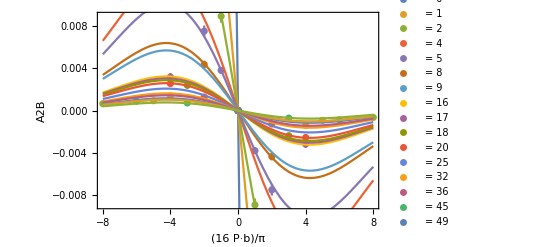

-0.0723521

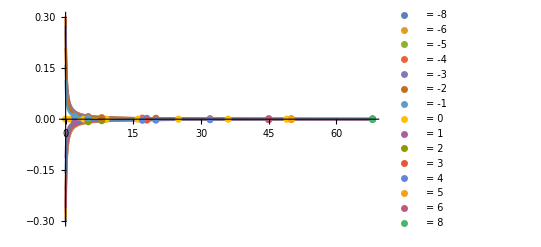

```mathematica
FitImAfordiffBPbbsq[A2B, -1, 8, modelsechfitIm]
```

```mathematica
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

```mathematica
SiversShift[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B},
dataforfitA12B = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{Pb32by2Pi, bsquare,data}];
dataforfitA2B = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{Pb32by2Pi, bsquare,data}];
(*Print[" for  is removed!"];
dataforfitA2B = Select[dataforfitA2B,#[[2]]!=0&];*)
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*Sech[b*x1]*(1/(c+x2));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*Sech[b*x1]*(1/(c+x2));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B,"\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=If[fitParasA12B[[2]][[1]]<0,-fitParasA12B[[2]],fitParasA12B[[2]]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=If[fitParasA2B[[2]][[1]]<0,-fitParasA2B[[2]],fitParasA2B[[2]]];
fitcA2B =fitParasA2B[[3]];
MassN = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
reducedratioA12B=(fitaA12B/(fitcA12B+b2II))*(II/(2*fitbA12B));
fourierA12B[x_, {reducedr_, bA12B_, cA12B_}] :=Sech[((N[Pi]*x)/(2*bA12B))]*reducedr;
reducedratioA2B=(fitaA2B/(fitcA2B+b2II))*(II/(2*fitbA2B));
fourierA2B[x_, {reducedr_, bA2B_, cA2B_}] :=Sech[((N[Pi]*x)/(2*bA2B))]*reducedr;
reducedratio1 = -MassN*(197*0.0001/lata)*reducedratioA12B/reducedratioA2B;
siversratio[x_, {reducedr1_, bA12B_, bA2B_}] := reducedr1*(Sech[((N[Pi]*x)/(2*bA12B))]/Sech[((N[Pi]*x)/(2*bA2B))]);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];
fourierA12Bforx = modelfitJackkifex[fourierA12B,{reducedratioA12B, fitbA12B, fitcA12B}, x];
fourierA2Bforx = modelfitJackkifex[fourierA2B,{reducedratioA2B, fitbA2B, fitcA2B}, x];
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A12BPltrangMax}}];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];
];
```

Fitting:    -> () = {⟨-0.0893(56)⟩_(2902J), ⟨-1.95(69)⟩_(2902J), ⟨0.073(36)⟩_(2902J)}, chisquareDoF = 13.9337
 Fitting:    -> () = {⟨0.3547(35)⟩_(2902J), ⟨0.1971(37)⟩_(2902J), ⟨0.5630(28)⟩_(2902J)}, chisquareDoF = 149.779
  = 9  = -2 ,eta = 8

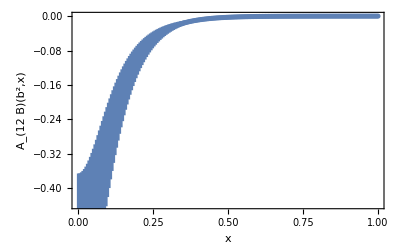

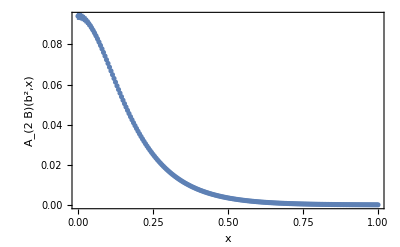

Sivers shift in GeV

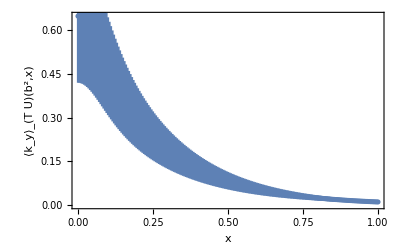

```mathematica
SiversShift[9,-2, 8]
```

Fitting:    -> () = {⟨-0.0548(80)⟩_(2902J), ⟨226.9(39)⟩_(2902J), ⟨0.046(83)⟩_(2902J)}, chisquareDoF = 4.48647
 Fitting:    -> () = {⟨0.3026(58)⟩_(2902J), ⟨-0.1384(46)⟩_(2902J), ⟨0.4863(46)⟩_(2902J)}, chisquareDoF = 48.5058
  = 9  = -3 ,eta = 8

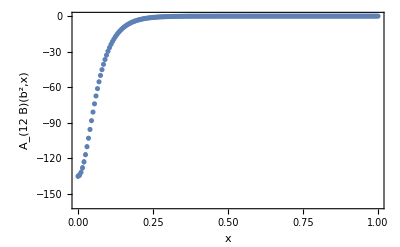

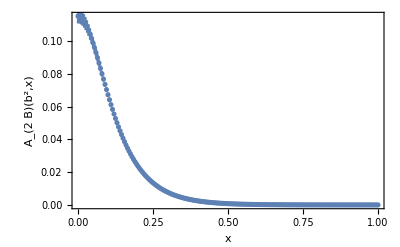

Sivers shift in GeV

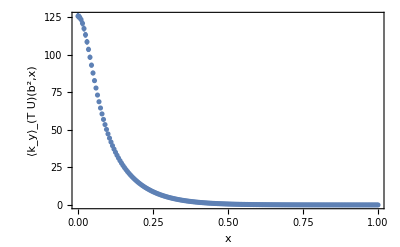

```mathematica
SiversShift[9,-3, 8]
```

Fitting:    -> () =                                                           6
{⟨-0.016(19)⟩_(2902J), ⟨-1.8(18) × 10 ⟩_(2902J), ⟨-1.2(12)⟩_(2902J)}, chisquareDoF = 1.42958
 Fitting:    -> () =                                                            3
{⟨11.86(23)⟩_(2902J), ⟨-110.1(33) × 10 ⟩_(2902J), ⟨18.07(35)⟩_(2902J)}, chisquareDoF = 2704.36
  = 9  = -4 ,eta = 8

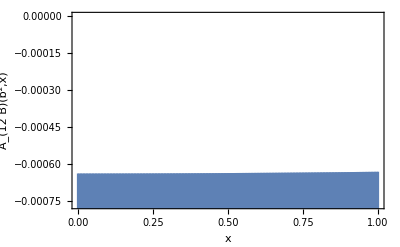

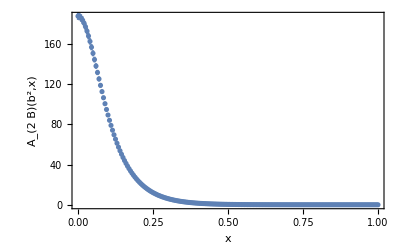

Sivers shift in GeV

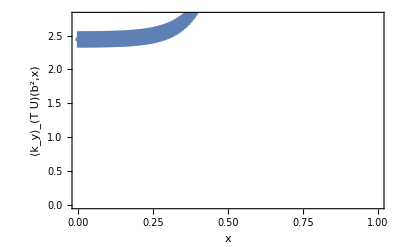

```mathematica
SiversShift[9,-4, 8]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

LinearAlgebra`BLAS`TRSV::oflow: Machine overflow encountered during computations.

General::stop: Further output of LinearAlgebra`BLAS`TRSV::oflow will be suppressed during this calculation.

General::munfl: Sech[-1740.57] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Sech[-1446.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Sech[-799.747] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Fitting:    -> () =                                                           6
{⟨0.200(83)⟩_(2902J), ⟨-300(220) × 10 ⟩_(2902J), ⟨10.6(41)⟩_(2902J)}, chisquareDoF = 4.03901

Fitting:    -> () =                                                            3
{⟨-12.92(23)⟩_(2902J), ⟨179.1(33) × 10 ⟩_(2902J), ⟨-19.68(35)⟩_(2902J)}, chisquareDoF = 3483.25

= 9  = -4 ,eta = 8

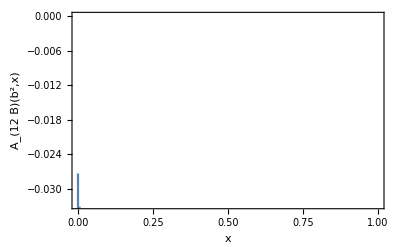

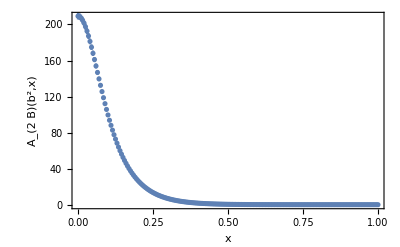

Sivers shift in GeV

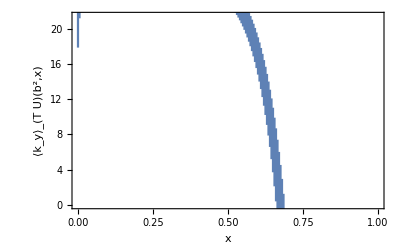

```mathematica
SiversShift[9,-4, 8]
```

```mathematica
SiversShiftgaussianfit[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B},
dataforfitA12B = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue}],{Pb32by2Pi, bsquare,data}];
dataforfitA2B = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue}],{Pb32by2Pi, bsquare,data}];
(*Print[" for  is removed!"];
dataforfitA2B = Select[dataforfitA2B,#[[2]]==9&];*)
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*Exp[-b*x1^2]*(1/(c+x2));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*Exp[-b*x1^2]*(1/(c+x2));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B];
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B =fitParasA12B[[2]];(**(32/(2N[Pi]))^2;*)
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B =fitParasA2B[[2]];(**(32/(2N[Pi]))^2;*)
fitcA2B =fitParasA2B[[3]];
MassN = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue}],MN][[1]];
reducedratioA12B=(fitaA12B/(2*Sqrt[N[Pi]*fitbA12B]*(fitcA12B+b2II)));
fourierA12B[x_, {reducedr_, bA12B_, cA12B_}] :=Exp[-((x^2)/(4*bA12B))]*reducedr;
reducedratioA2B=(fitaA2B/(2*Sqrt[N[Pi]*fitbA12B]*(fitcA2B+b2II)));
fourierA2B[x_, {reducedr_, bA2B_, cA2B_}] :=Exp[-((x^2)/(4*bA2B))]*reducedr;
reducedratio1 = -MassN*(197*0.0001/lata)*reducedratioA12B/reducedratioA2B;
siversratio[x_, {reducedr1_, bA12B_, bA2B_}] := reducedr1*(Exp[-((x^2)/(4*bA12B))]/Exp[-((x^2)/(4*bA2B))]);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];
fourierA12Bforx = modelfitJackkifex[fourierA12B,{reducedratioA12B, fitbA12B, fitcA12B}, x];
fourierA2Bforx = modelfitJackkifex[fourierA2B,{reducedratioA2B, fitbA2B, fitcA2B}, x];
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
Print[ "  = ",b2, "  = ",P1," ,eta = ", etavalue];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A12BPltrangMax}}];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A2BPltrangMax}}];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]+MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{SsPltrangMax,0}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift]
];
```

Fitting:    -> () = {⟨-0.0465(39)⟩_(2902J), ⟨0.0191(91)⟩_(2902J), ⟨0.493(78)⟩_(2902J)}, chisquareDoF = 32.7582

Fitting:    -> () = {⟨0.2001(13)⟩_(2902J), ⟨0.0665(18)⟩_(2902J), ⟨0.6342(20)⟩_(2902J)}, chisquareDoF = 4857.7

= 9  = -1 ,eta = 8

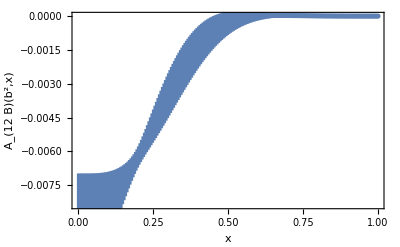

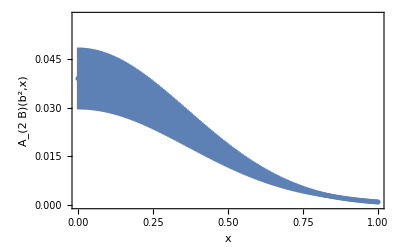

Sivers shift in GeV

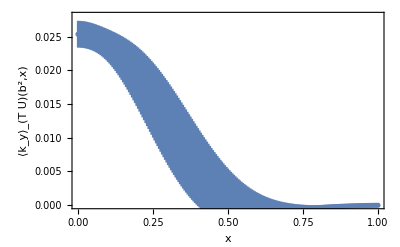

```mathematica
SiversShiftgaussianfit[9,-1,8]
```

Fitting:    -> () = {⟨-0.0450(29)⟩_(2902J), ⟨0.0088(24)⟩_(2902J), ⟨0.083(37)⟩_(2902J)}, chisquareDoF = 53.2372

Fitting:    -> () = {⟨0.1768(18)⟩_(2902J), ⟨0.01730(64)⟩_(2902J), ⟨0.5614(28)⟩_(2902J)}, chisquareDoF = 1916.86

= 9  = -2 ,eta = 8

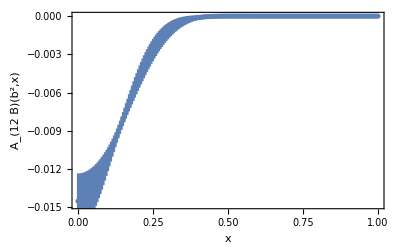

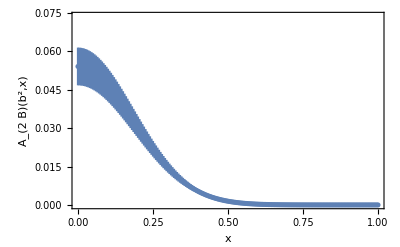

Sivers shift in GeV

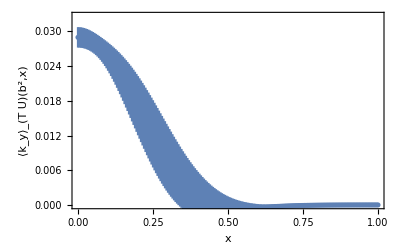

```mathematica
SiversShiftgaussianfit[9,-2,8]
```

Fitting:    -> () = {⟨0.0200(42)⟩_(2902J), ⟨0.0004 ± 0.0023⟩_(2902J), ⟨0.02 ± 0.15⟩_(2902J)}, chisquareDoF = 5.72968

Fitting:    -> () = {⟨0.1510(29)⟩_(2902J), ⟨0.00858(55)⟩_(2902J), ⟨0.4853(46)⟩_(2902J)}, chisquareDoF = 491.481

= 9  = -3 ,eta = 8

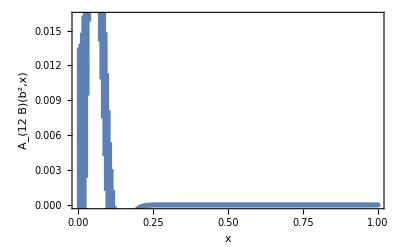

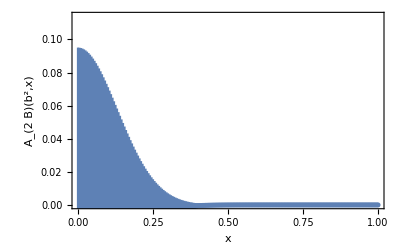

Sivers shift in GeV

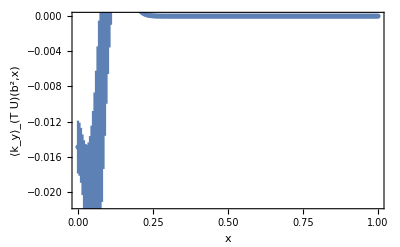

```mathematica
SiversShiftgaussianfit[9,-3,8]
```